```mathematica
ClearAll["Global`*"];

(*local truncation*)
nMax=2;                 (*Fock levels 0,1,2*)
d=nMax+1;          (*local Hilbert space dimension*)
mMass=1.0;               (*"mass" in kinetic term*)

(*creation/annihilation in number basis*)
a=Table[If[n==m+1,Sqrt[m],0],{n,0,nMax},{m,0,nMax}];
ad=ConjugateTranspose[a];

xSingle=(a+ad)/Sqrt[2 mMass];
pSingle=I Sqrt[mMass/2] (ad-a);

idSite=IdentityMatrix[d];

(*quick debug:dimensions*)
Dimensions/@{a,xSingle,pSingle}
```

{{3,3},{3,3},{3,3}}

```mathematica
Nsites=5;

opOnSite[op_,j_]:=KroneckerProduct@@Table[If[k==j,op,idSite],{k,1,Nsites}];

xOp[j_]:=opOnSite[xSingle,j];
pOp[j_]:=opOnSite[pSingle,j];

dimHilbert=d^Nsites
Dimensions[xOp[3]]
```

243

{243,243}

```mathematica
β=1.0;
μCos=0.5;        (*strength of cos potential*)
κ=0.1;        (*gradient coupling*)

(*cos(β x) on a single site*)
cosPhiSingle=MatrixFunction[Cos,β xSingle];
VsiteSingle=μCos^2 (idSite-cosPhiSingle);  (* ~μ^2 (1-cos βφ)*)

(*embed on chain*)
Vsite[j_]:=opOnSite[VsiteSingle,j];
```

```mathematica
Dimensions[VsiteSingle]
Dimensions[Vsite[2]]
```

{3,3}

{243,243}

```mathematica
(*kinetic+mass term*)Hkin=Sum[1/2 pOp[j].pOp[j]+1/2 mMass^2 xOp[j].xOp[j],{j,1,Nsites}];

(*gradient term (nearest-neighbour)*)
Hgrad=(κ/2) Sum[(xOp[j+1]-xOp[j]).(xOp[j+1]-xOp[j]),{j,1,Nsites-1}];

(*cosφ potential on each site*)
Hcos=Sum[Vsite[j],{j,1,Nsites}];

H0=Hkin+Hgrad+Hcos;

Dimensions[H0]
```

{243,243}

```mathematica
J0=1.0;   (*strong initial string*)
JFinal=0.2;   (*weaker string after quench*)

JvecInit={0,J0,J0,J0,0};
JvecFinal={0,JFinal,JFinal,JFinal,0};

Hsource[vec_]:=Sum[vec[[j]] xOp[j],{j,1,Nsites}];

Hinit=H0+Hsource[JvecInit];
Hfinal=H0+Hsource[JvecFinal];

Dimensions/@{Hinit,Hfinal}
```

{{243,243},{243,243}}

```mathematica
{evalsInit,evecsInit}=Eigensystem[N[Hinit]];

ord=Ordering[evalsInit];
E0Init=evalsInit[[ord[[1]]]];
psi0=Normalize[evecsInit[[ord[[1]]]]];

{E0Init,Norm[psi0]}
```

{-0.391504+0. ⅈ,1.}

```mathematica
{evalsFinal,evecsFinal}=Eigensystem[N[Hfinal]];
Udag=ConjugateTranspose[evecsFinal];

(*initial state in eigenbasis of Hfinal*)
psi0Eig=Udag.psi0;

(*x_j in eigenbasis of Hfinal*)
xEig[j_]:=Udag.xOp[j].evecsFinal;

(*time-evolved state in eigenbasis*)
psiEig[t_]:=DiagonalMatrix[Exp[-I evalsFinal t]].psi0Eig;

xExp[j_,t_]:=Module[{psi=psiEig[t]},Re[Conjugate[psi].(xEig[j].psi)]];
```

```mathematica
xExp[3,0.]
```

-0.707107

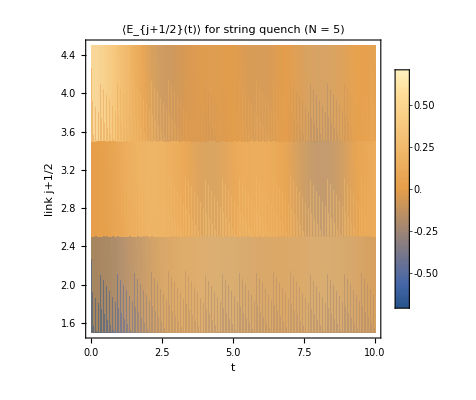

```mathematica
EExp[j_,t_]:=xExp[j+1,t]-xExp[j,t];  (*link between j and j+1*)

tmax=10;
dt=0.1;

(*build {t,linkPosition,E} triples for links 1..4*)
dataE=Flatten[Table[{t,j+0.5,EExp[j,t]},{j,1,Nsites-1},{t,0,tmax,dt}],1];

ListDensityPlot[dataE,FrameLabel->{"t","link j+1/2"},PlotLabel->"⟨E_{j+1/2}(t)⟩ for string quench (N = 5)",PlotLegends->Automatic]
```

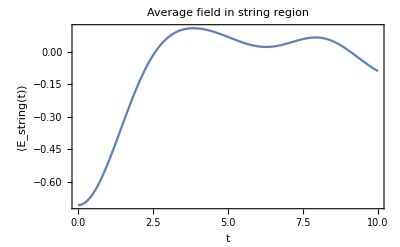

```mathematica
(*average field in central string region:links 2 and 3*)Estring[t_]:=xExp[3,t];

Plot[Estring[t],{t,0,tmax},Frame->True,FrameLabel->{"t","⟨E_string(t)⟩"},PlotLabel->"Average field in string region"]
```